```mathematica
SetDirectory[NotebookDirectory[]];
```

# Plot options for notebook

```mathematica
imgsize=400;
```

```mathematica
SetOptions[ListContourPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30},ImageSize->imgsize}];
SetOptions[ListLinePlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->18},ImageSize->imgsize}];
SetOptions[ListPlot3D,{PlotTheme->"Scientific",BaseStyle->{FontSize->18},ImageSize->imgsize}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
colorFunc=("DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListContourPlot]));
```

# Spatial Galton-Watson system - Variational terms

Setup

### Nu domain

```mathematica
nuLength=21;
```

```mathematica
nuMin=-1.0;
nuMax=4.0;
```

```mathematica
deltanu=(nuMax-nuMin)/(nuLength-1);
```

```mathematica
nuGrid=Table[i,{i,nuMin,nuMax,(nuMax-nuMin)/(nuLength-1)}];
```

### Which nuVary to evaluate at

```mathematica
nuVaryGrid={1.0};
nuVaryLength=Length[nuVaryGrid];
```

### y domain

```mathematica
yLength=50;
```

```mathematica
yMin=-0.5;
yMax=0.5;
```

```mathematica
deltay=(yMax-yMin)/(yLength-1);
```

```mathematica
yGrid=Table[i,{i,yMin,yMax,(yMax-yMin)/(yLength-1)}];
```

### Set Max time T and increment Delta t

```mathematica
tMax=1.5*10^(-2);
deltat=tMax/100.0;
tLength=IntegerPart[tMax/deltat]+1;
```

```mathematica
tGrid=Table[i,{i,0,tMax,deltat}];
```

### Diff constant

```mathematica
dc=1.0;
```

Helper functions

### True solution

```mathematica
f1True[onu_]:=-dc;
f2True[onu_]:=dc;
```

### onu from average

```mathematica
onuFromAve[an_,aSpatial_]:=-Log[aSpatial/an];
```

### Initial condition of gaussian centered at some y

```mathematica
onuIC[yCenter_,aven_]:=Module[
{myZero,var,onu0,checkNorm}
,
myZero=10^(-10);
var=0.05;
onu0=Table[onuFromAve[aven,Exp[-(yGrid[[iy]]-yCenter)^2/var]],{iy,2,yLength-1}]//N;
onu0=Join[{onu0[[1]]},onu0,{onu0[[-1]]}];
checkNorm=deltay*Sum[Exp[-onu0[[iy]]],{iy,1,yLength}];
onu0+=ConstantArray[Log[checkNorm],yLength];
Return[onu0]
];
```

#### Check

```mathematica
onuICtest=onuIC[0.0,10]
```

{3.67376,3.67376,3.29059,2.92408,2.57422,2.24103,1.92449,1.62462,1.3414,1.07485,0.824951,0.591715,0.375139,0.175222,-0.00803515,-0.174632,-0.32457,-0.457848,-0.574466,-0.674424,-0.757723,-0.824362,-0.874341,-0.90766,-0.92432,-0.92432,-0.90766,-0.874341,-0.824362,-0.757723,-0.674424,-0.574466,-0.457848,-0.32457,-0.174632,-0.00803515,0.175222,0.375139,0.591715,0.824951,1.07485,1.3414,1.62462,1.92449,2.24103,2.57422,2.92408,3.29059,3.67376,3.67376}

```mathematica
checkNorm=deltay*Sum[Exp[-onuICtest[[iy]]],{iy,1,yLength}]
```

1.

```mathematica
onuICtestInterp=Interpolation[Table[{yGrid[[iy]],onuICtest[[iy]]},{iy,1,yLength}],InterpolationOrder->1];
```

### Trajectory of onu, perturbing f1 or f2 at some idx

```mathematica
onuTrajPerturb[f1Interp_,f2Interp_,oeta_,onuVary_,mag_,fVaryIdx_]:=Module[
{perturbVar,eq1,bc1,bc2,bc3,sol,maxTime,nuSt,iMax}
,
perturbVar=0.01;
If[
fVaryIdx==1,
eq1=D[onu[y,t],t]==(f1Interp[onu[y,t]]+mag*Exp[-(onu[y,t]-onuVary)^2/perturbVar])*(D[onu[y,t],y])^2+f2Interp[onu[y,t]]*D[onu[y,t],{y,2}],
eq1=D[onu[y,t],t]==f1Interp[onu[y,t]]*(D[onu[y,t],y])^2+(f2Interp[onu[y,t]]+mag*Exp[-(onu[y,t]-onuVary)^2/perturbVar])*D[onu[y,t],{y,2}]
];

bc1=onu[y,0]==oeta[y];
bc2=Derivative[1,0][onu][yMin,t]==oeta'[yMin];
bc3=Derivative[1,0][onu][yMax,t]==oeta'[yMax];

sol=Quiet[NDSolve[{
eq1,
bc1,
bc2,
bc3,
WhenEvent[Max[onu[y,t]/.y->"ValuesOnGrid"]>=nuMax,"StopIntegration"],
WhenEvent[Min[onu[y,t]/.y->"ValuesOnGrid"]<=nuMin,"StopIntegration"]
},
onu,{y,yMin,yMax},{t,0,tMax},
Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->50000,"MaxPoints"->50000}}
]][[1]];

maxTime=(onu/.sol/.InterpolatingFunction[{a_,b_},__]:>b)[[2]];
nuSt={};
Do[
AppendTo[nuSt,Table[(onu/.sol)[yVal,tVal],{yVal,yGrid}]];
,{tVal,0,maxTime,deltat}];

Return[nuSt]
];
```

### Solve var term

```mathematica
solveVarTerm[f1Interp_,f2Interp_,oeta_]:=Module[
{numag,nnu,interpOrder,r1true,r2true,nuTrajPerturb1,nuLengthPerturb1,nuTrajPerturb2,nuLengthPerturb2,nuLength,tbl,tblinterp,tblder,lengthTest,dim1,dim2,deleteList,ctr}
,
numag=10^(-2);
nnu=10;
interpOrder=5;

(* 
Store r1,r2,
first level = time, 
second = pos in nu space to vary at, 
third = y in numerator 
*)
r1true=Association[];
r2true=Association[];

(* Go through all nu to vary at *)
Do[
Print["Varying at: nu = ",nuVary," out of ",nuVaryGrid];

(* Solve for nu trajectory for different perturbations *)
nuTrajPerturb1=Association[];
nuLengthPerturb1=Association[];
nuTrajPerturb2=Association[];
nuLengthPerturb2=Association[];
ctr=0;
Monitor[
Do[
ctr+=1;
nuTrajPerturb1[nuVaryMag]=onuTrajPerturb[f1Interp,f2Interp,oeta,nuVary,nuVaryMag,1];
nuLengthPerturb1[nuVaryMag]=Length[nuTrajPerturb1[nuVaryMag]];
nuTrajPerturb2[nuVaryMag]=onuTrajPerturb[f1Interp,f2Interp,oeta,nuVary,nuVaryMag,2];
nuLengthPerturb2[nuVaryMag]=Length[nuTrajPerturb2[nuVaryMag]];
,{nuVaryMag,-nnu*numag,nnu*numag,numag}];
,
ProgressIndicator[ctr,{1,2*nnu+1}]
];

(* Max length before we go off grid *)
nuLength=Min[Min[Values[nuLengthPerturb1]],Min[Values[nuLengthPerturb2]]];

(* Go through all times *)
Do[
Do[
(* R1 *)
tbl=Table[{nuVaryMag,nuTrajPerturb1[nuVaryMag][[it,iy]]},{nuVaryMag,-nnu*numag,nnu*numag,numag}];
tblinterp=Interpolation[tbl,InterpolationOrder->interpOrder];
tblder=Derivative[1][tblinterp];
If[!KeyExistsQ[r1true,it],r1true[it]=Association[];];
If[!KeyExistsQ[r1true[it],nuVary],r1true[it][nuVary]=Association[];];
r1true[it][nuVary][iy]=tblder[0.0];

(* R2 *)
tbl=Table[{nuVaryMag,nuTrajPerturb2[nuVaryMag][[it,iy]]},{nuVaryMag,-nnu*numag,nnu*numag,numag}];
tblinterp=Interpolation[tbl,InterpolationOrder->interpOrder];
tblder=Derivative[1][tblinterp];
If[!KeyExistsQ[r2true,it],r2true[it]=Association[];];
If[!KeyExistsQ[r2true[it],nuVary],r2true[it][nuVary]=Association[];];
r2true[it][nuVary][iy]=tblder[0.0];
,{it,1,tLength}];
,{iy,1,yLength}];

,{nuVary,nuVaryGrid}];

(* Fix such that at all times, the dimensions all exist *)
(*
dim1=Length[r1true[0]];
dim2=Length[r1true[0][nuGrid[[1]]]];
deleteList={};
Do[
If[Length[r1true[it]]≠dim1||Length[r2true[it]]≠dim1
,
deleteList=Append[deleteList,it];
,
Do[
If[Length[r1true[it][nuVary]]≠dim2||Length[r2true[it][nuVary]]≠dim2
,
deleteList=Append[deleteList,it];
Break[];
];
,{nuVary,nuGrid}];
];
,{it,1,tLength}];
r1true=KeyDrop[r1true,deleteList];
r2true=KeyDrop[r2true,deleteList];
*)
Return[{r1true,r2true}];
];
```

### Trajectory of onu

```mathematica
onuTraj[f1Interp_,f2Interp_,oeta_]:=onuTrajPerturb[f1Interp,f2Interp,oeta,nuMin,0.0,1];
```

Test

#### Test

```mathematica
onuTrajTest=onuTrajPerturb[f1True,f2True,onuICtestInterp,1.0,10^-3,1];
```

```mathematica
Manipulate[ListLinePlot[onuTrajTest[[it]],PlotRange->{Min[onuTrajTest[[1]]],Max[onuTrajTest[[1]]]}],{it,1,Length[onuTrajTest],1},SaveDefinitions->True]
```

```mathematica
Manipulate[ListLinePlot[Exp[-onuTrajTest[[it]]],PlotRange->{0,3}],{it,1,tLength,1},SaveDefinitions->True]
```

Run

### IC

```mathematica
onuICtest=onuIC[0.0,10]
```

{3.67376,3.67376,3.29059,2.92408,2.57422,2.24103,1.92449,1.62462,1.3414,1.07485,0.824951,0.591715,0.375139,0.175222,-0.00803515,-0.174632,-0.32457,-0.457848,-0.574466,-0.674424,-0.757723,-0.824362,-0.874341,-0.90766,-0.92432,-0.92432,-0.90766,-0.874341,-0.824362,-0.757723,-0.674424,-0.574466,-0.457848,-0.32457,-0.174632,-0.00803515,0.175222,0.375139,0.591715,0.824951,1.07485,1.3414,1.62462,1.92449,2.24103,2.57422,2.92408,3.29059,3.67376,3.67376}

```mathematica
checkNorm=deltay*Sum[Exp[-onuICtest[[iy]]],{iy,1,yLength}]
```

1.

```mathematica
onuICtestInterp=Interpolation[Table[{yGrid[[iy]],onuICtest[[iy]]},{iy,1,yLength}],InterpolationOrder->1];
```

### Generate var term traj

```mathematica
{r1True,r2True}=solveVarTerm[f1True,f2True,onuICtestInterp];
```

Varying at: nu = 1. out of {1.}

# Plots

R1, R2 as a func of y, nuVary

```mathematica
r1TruePlot=Association[];
r2TruePlot=Association[];
Do[
r1TruePlot[it]=Flatten[Table[{yGrid[[iy]],nuVary,r1True[it][nuVary][iy]},{iy,1,yLength},{nuVary,nuGrid}],1];
r2TruePlot[it]=Flatten[Table[{yGrid[[iy]],nuVary,r2True[it][nuVary][iy]},{iy,1,yLength},{nuVary,nuGrid}],1];
,{it,1,tLength}];
```

```mathematica
Manipulate[ListContourPlot[r1TruePlot[it],PlotLegends->Automatic,PlotRange->{0,0.1}],{it,1,tLength,1}]
```

ListContourPlot::arrayerr: Global`r1TruePlot[1.] must be a valid array.

```mathematica
Manipulate[ListContourPlot[r2TruePlot[it],PlotLegends->Automatic],{it,1,tLength,1}]
```

ListContourPlot::arrayerr: Global`r2TruePlot[1.] must be a valid array.

True solution

```mathematica
onuTrue=onuTraj[f1True,f2True,onuICtestInterp];
```

```mathematica
Manipulate[ListLinePlot[Transpose[{yGrid,onuTrue[[it]]}],PlotRange->{-1,4}],{it,1,tLength,1}]
```

Part::partd: Part specification Global`onuTrue⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Global`yGrid,Global`onuTrue⟦1⟧} cannot be transposed.

Part::partd: Part specification Global`onuTrue⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {Global`yGrid,Global`onuTrue⟦1⟧} cannot be transposed.

ListLinePlot::lpn: Transpose[{Global`yGrid,Global`onuTrue⟦1⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
onuTrueGrid=Flatten[Table[{yGrid[[iy]],tGrid[[it]],onuTrue[[it,iy]]},{iy,1,yLength},{it,1,tLength}],1];
```

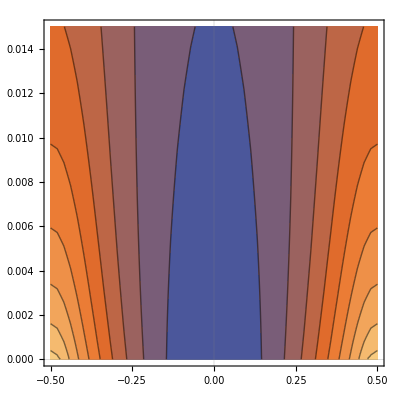

```mathematica
ListContourPlot[onuTrueGrid]
```

```mathematica
nuVaryChoose=nuGrid[[9]]
```

1.

```mathematica
nuVaryGrid=Flatten[Table[{yGrid[[iy]],tGrid[[it]],nuVaryChoose},{iy,1,yLength},{it,1,tLength}],1];
```

```mathematica
Show[
ListPlot3D[onuTrueGrid],
ListPlot3D[nuVaryGrid]
]
```

-Graphics3D-

R, onu as a func of time, at a single y, nuvary

```mathematica
iyChoose=8;
yChoose=yGrid[[iyChoose]]
```

-0.357143

```mathematica
nuVaryChoose=nuGrid[[9]]
```

1.

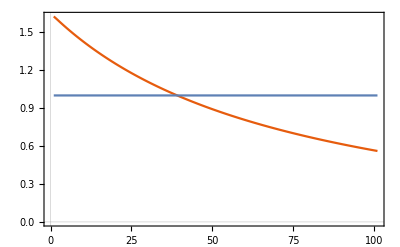

```mathematica
Show[
ListLinePlot[onuTrue[[;;,iyChoose]]]
,
Plot[nuVaryChoose,{i,1,tLength}]
]
```

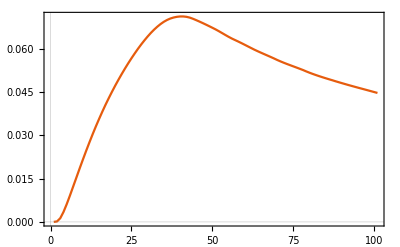

```mathematica
ListLinePlot[Table[r1True[it][nuVaryChoose][iyChoose],{it,1,tLength}]]
```

R, onu as a func of time, for several y values, at a single nuvary

```mathematica
iyChoose=Table[i,{i,6,9}];
stackStyles=Table[ColorData["AlpineColors",i/10.0],{i,1,4}];
```

```mathematica
nuVaryChoose=nuGrid[[9]]
```

1.

```mathematica
(* determine vertical lines by intersections with trajectories of nu *)
pltvert={};
Do[
nuTrajTmp=Table[{tGrid[[it]],onuTrue[[it,iy]]},{it,1,tLength}];
Do[
If[nuTrajTmp[[i+1,2]]<nuVaryChoose&&nuTrajTmp[[i,2]]>nuVaryChoose,
{tAbove,nuAbove}=nuTrajTmp[[i]];
{tBelow,nuBelow}=nuTrajTmp[[i+1]];
Break[];
];
,{i,1,Length[nuTrajTmp]-1}];

frac=(nuVaryChoose-nuAbove)/(nuBelow-nuAbove);
tCross=tAbove+frac*(tBelow-tAbove);

AppendTo[pltvert,
ListLinePlot[{{tCross,-1.0},{tCross,4.0}},PlotStyle->{LightGray,Dashed}]
];

,{iy,iyChoose}];
```

```mathematica
plthorz=Plot[nuVaryChoose,{i,0,tMax},PlotStyle->{LightGray,Dashed}];
```

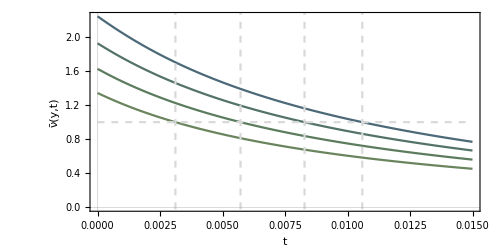

```mathematica
pltnustack=Show[
ListLinePlot[Table[{tGrid[[it]],onuTrue[[it,iy]]},{iy,iyChoose},{it,1,tLength}],PlotStyle->stackStyles,FrameLabel->{"t","ν̄(y,t)"},Frame->True]
,
plthorz
,
pltvert
,
ImageSize->500
,
AspectRatio->0.5
]
```

```mathematica
Export["../figures_gw_spatial/nu_stack.pdf",pltnustack]
```

../figures_gw_spatial/nu_stack.pdf

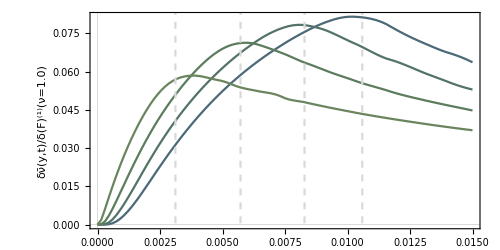

```mathematica
pltr1stack=Show[
ListLinePlot[Table[{tGrid[[it]],r1True[it][nuVaryChoose][iy]},{iy,iyChoose},{it,1,tLength}],PlotStyle->stackStyles,Frame->True,FrameLabel->{Automatic,"δν̄(y,t)/δ(F̄)^(1)(ν=1.0)"},FrameTicksStyle->{Automatic,Directive[FontOpacity->0]},ImageSize->500,AspectRatio->0.5]
,
pltvert
]
```

```mathematica
Export["../figures_gw_spatial/r1_stack.pdf",pltr1stack]
```

../figures_gw_spatial/r1_stack.pdf

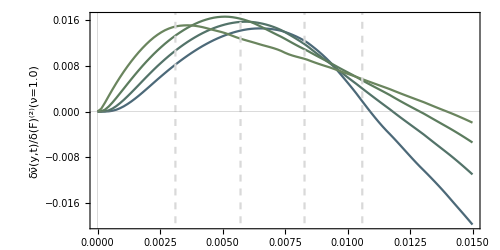

```mathematica
pltr2stack=Show[
ListLinePlot[Table[{tGrid[[it]],r2True[it][nuVaryChoose][iy]},{iy,iyChoose},{it,1,tLength}],PlotStyle->stackStyles,Frame->True,FrameLabel->{Automatic,"δν̄(y,t)/δ(F̄)^(2)(ν=1.0)"},FrameTicksStyle->{Automatic,Directive[FontOpacity->0]},ImageSize->500,AspectRatio->0.5]
,
pltvert
]
```

```mathematica
Export["../figures_gw_spatial/r2_stack.pdf",pltr2stack]
```

../figures_gw_spatial/r2_stack.pdf